# DarkMoreEverything

## By: Tone

## Introduction

## Description

The aim of this project is to have a complete dark mode throughout all of Mathematica and its various components that does not restrict any features or functionality. Whilst the project has not yet reached 100% coverage, it far exceeds the coverage of all other dark themes publicly available, and has no known functionality constraints. The project has also evolved to include general front end functionality extensions and improvements.

## Installation

### 1. Backup

Prior to installation, you should backup your “SystemFiles” folder inside “$InstallationDirectory”.

#### DME Palette

#### Manual

### 2. Replace existing files

Replace the existing files inside “$InstallationDirectory/SystemFiles” with the ones found inside “DarkModeEverything/SystemFiles”.

#### DME Palette

#### Manual

### 3. Set defaults

Set DarkModeEverything.nb as the default global StyleDefinitions

#### DME Palette

##### fdgf

#### Manual

## Cell Styles

This section lists examples of most commonly used cell styles including any shortcuts used to generate one.

Key:

CellStyle [ shortcut1 | shortcut2 ]- “ [ ] ” contain different shortcuts separated by “ | ” to generate a cell .

Shortcuts can take 2 main forms:

Alt + NumberRowKey

NumberRowKey is a number from the keyboards number row

Eg. Style1 [ Alt + Num ]:
	Pressing Alt+Num inside any cell will change that cell to Style1
	(Or generate a new Style1 cell if cell insertion line is selected)

CellStyle + Key

CellStyle is an existing cell style

Key is any keyboard key

Eg. Style1 [ Style2 + Key ],
	Pressing Key inside a cell of style Style2 will change that cell into a Style1 cell

Note: Any [ Input + Key ] shortcut will work when inputting a new cell in the cell insertion line.

Examples

# Title [ Alt+1 ]

## Subtitle [ Alt+2 ]

## Chapter [ Alt+3 ]

## Section [ Alt+4 ]

### Subsection [ Alt+5 ]

#### Subsubsection [ Alt+6 ]

##### Subsubsubsection

Text [ Alt + 7 ]

Item [ Text+Tab | Text+* | Subitem+Backspace ]

Subitem [ Item+Tab | Item+* | Subsubitem+Backspace ]

Subsubitem [ Subitem+Tab | Subitem+* ]

```mathematica
"Code [ Alt+8 | Input+` ]"
```

"InitialisationCell [ Code+Tab ]"

```mathematica
"Input [ Alt+9 | Code+` ]"
```

Print

PrintTemporary

Echo

EchoTiming

Output

Purple delimiter [ Input+- ]

ExternalLanguage [ Input+> ]

NLInput [ Input+= ]

WolframAlphaInput [ NLInput+= ]

## Example outputs

## Entities

```mathematica
Quantity[12, "Meters"]
```

```mathematica
Entity["Country","UnitedKingdom"][EntityProperty["Country","AdministrativeDivisions"]]
```

```mathematica
EntityClass["Country","EuropeanUnion"][EntityPropertyClass["Country","EconomicProperties"]]
```

## Dataset

```mathematica
ExampleData[{"Dataset","Planets"}]
```

## Plots

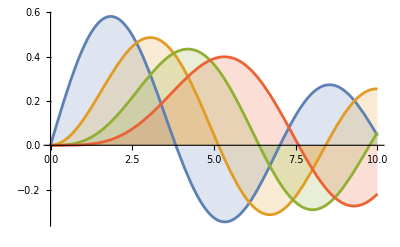

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

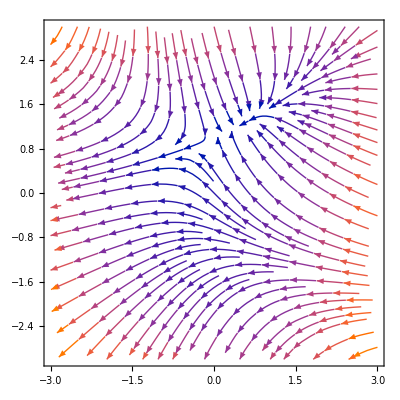

```mathematica
StreamPlot[{-1-x^2+y,1+x-y^2},{x,-3,3},{y,-3,3}]
```

```mathematica
DiscretePlot3D[{PDF[MultivariatePoissonDistribution[3,{1,1}],{t,u}],PDF[MultivariatePoissonDistribution[5,{2,2}],{t,u}]},{t,0,10},{u,0,10},ExtentSize->Full]
```

-Graphics3D-

## Manipulate

```mathematica
Manipulate[]
```

## NaturalLanguageInput

WolframAlphaQueryParseResults

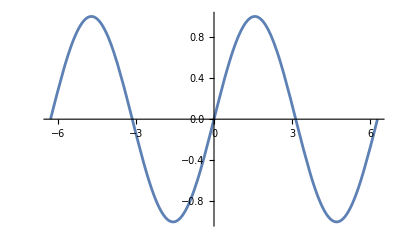

## WolframAplphaInput

Denmark

WolframAlphaQueryResults

## Context coloring

Quiet[
	Other`Symbol = 0;
	Global`Symbol= 0;
]

Global`Symbol::shdw: Symbol Symbol appears in multiple contexts {Global`,System`}; definitions in context Global` may shadow or be shadowed by other definitions.

```mathematica
Undefined`Symbol
System`Symbol
Global`Symbol
Other`Symbol
```

## Extended coverage

## Documentation

The documentation is completely covered by this dark theme’s custom Reference.nb stylesheet. The styling uses the same design language as the main notebooks and restricts NO functionality, covering all sections of the documentation.

The following hyperlinks showcase some of the changes to the different documentation sections:

Function documentation

Entity documentation

Tech Notes

Monographs

## Message window

The Mathematica message window has also been changed according to the dark theme.

```mathematica
(*
	Evaluation of this cell generates a
	message inside the message window
*)
SessionSubmit[
	1/0
];
```

## Wolfram Chatbooks

DME comes with a dark Chatbook.nb stylesheet.

```mathematica
CreateNotebook["ChatEnabled"];
```

## Testing notebooks

DME comes with a dark MUnit.nb stylesheet used in testing notebooks.

```mathematica
CreateNotebook["Testing"];
```

## Stylesheet theming

DME comes with a dark StylesheetFormatting.nb stylesheet which changes the theming of the stylesheet editor notebooks.

```mathematica
SystemOpen@
FileNameJoin[{$InstallationDirectory,"SystemFiles","FrontEnd","StyleSheets","DarkModeEverything.nb"}]
```

## Handy changes & additions

## NotebookAutoSave

The DME stylesheet enablesNotebookAutoSave which will attempt to save the notebook any time an evaluation is performed. This can give an error sound when evaluating a notebook which is not yet been saved, however, this does not impact functionality.

## Reset Dataset options

The Options for Dataset are changed upon initialisation of the DME stylesheet as to conform with the dark theming. However, these options can get rest to default when performing certain Dataset operations. Because of this, these is a convenient function defined in the stylesheet to reset dataset options back to either dark or light defaults.

Reset Dataset options to the dark defaults:

```mathematica
resetDatasetOptions[];
```

Reset DatasetOptions to default:

```mathematica
resetDatasetOptions[Automatic];
(* Or *)
resetDatasetOptions[Default];
```

## Map subscript level-spec

This is a shorthand implemented in the initialisation of the DME stylesheet to allow for quick level specification to Map’s “/@” abbreviation:

```mathematica
(* f(/@)_i list -> Map[f, list, {i}] *)
f (/@)_2 {1,1,{2,{3,3}}}
```

{1,1,{f[2],f[{3,3}]}}

## Outstanding items & known issues

As mentioned in the description, this project is very close to complete dark theme coverage within Mathematica, successfully, there are still some components that have yet to be successfully changed.
This could be due to either it being too difficult to make the changes, or more commonly, I didn’t quite get to them yet.
This section will list the biggest outstanding items:

WolframAlphaPod text on labels and plot axes are still not coherently themed. These font colors are handled inside the WolframAlphaClient.m source file and not through any StyleSheet defaults and as such, take a lot of time to track down and change. Since these colors do not impair usability, and more importantly, almost never use WolframAlphaInput, so these are on the “I should probably change these... some day” box.

The background of the workflow guides docked cell inside the documentation is still in a light theme. I have tried to track down the style of this docked cell to no avail. This one annoys me a lot and is one of the primary current TODOs although it is still perfectly usable.

Scrollbars and window menus are all tied to the OS so cannot be currently changed on windows 11, however, Windows 10 tied these colors to the registry and allows custom colors and also the Linux front end can accept a custom Qt file defining custom colors for WindowElements.